# NLP and large-scale information retrieval on mathematical texts

## Yihe Dong Wolfram Research

#WolframTechConf

## Task

Semantic representation of mathematical statements.

Theorem search from fast-growing body of knowledge.

## Task

Semantic representation of mathematical statements.

Theorem search from fast-growing body of knowledge.

Math + math-physics new papers by year on arXiv:

-Graphics-

(arxiv.org)

## Goals

Check if some proposition has been proved in the arXiv corpus.

Gather technical results about a specific research topic.

Bring up entire theorems that pertains to the query, for fast and easy navigation.

Able to find results even with different formulation.

Adequate parsing of TeX.

Theorem context retrieval.

Towards semantic representation for mathematical statements, .

## I. Theorem search

### Data

arXiv papers 1995 - present

~770K math and math physics papers

Extracted 2.4 million key statements: theorems, propositions, conjectures, etc.

## Challenges

Scale.

Sensible ranking.

Raw TeX very non-uniform.

## Three-pronged approach

Semantic representation for context-based search.

Words-based search.

Latent semantic analysis.

## Data processing

### Terms

23852 vocabulary word representatives. Selected based on frequency analysis.

n-grams

E.g. Dedekind domain

Singularization

E.g. matrices -> matrix

Word-stemming: trie of frequency distributions.

E.g annihilate, annihilator, annihilating -> annihilat

Related words: Trained bag-of-words neural net to create word embeddings.

E.g. nilpotent: [semisimply, unipotently, semisimple, unipotent, nilpotency, abelian, centraliser]

Synonyms, antonyms

E.g. abelian <--> commutative

## Data processing

### TeX

Extract theorems, lemmas, propositions, etc.

TeX processing, such as macros substitution.

Find definitions of symbols from surrounding text.

### Semantics

Parse extracted theorems and surrounding text.

### Metadata

Collect meta data on each theorem: authors, date, title, etc.

## Search implementation

### Words-based search

Term membership in theorems are precomputed.

Each term retrieves a list of theorems, take ranked intersection of these lists.

### Semantics-based search

Precompute parse of the theorems to create context vectors that record parent-child relations.

Rank based on number of coinciding relations.

### Latent semantic analysis

Truncated SVD:

Dimension reduction.

Consolidate terms that share semantic similarity.

Project from the 23852-dimensional feature space down to 35 dimensions.

M weighted, normalized, term-document matrix, with decomposition M→UDV^T.

Dimensions: M: 23852 × 49256; U: 23852 × 35; V^T: 35 × 49256; D: 35 x 35.

Given 23852-dimensional query vector v, project it down to 35 dimensions with v̂==D^-1 U^T v, and look for the nearest column vectors in corpus to v̂.

## Search implementation

### Words-based search

Term membership in theorems are precomputed.

Each term retrieves a list of theorems, take ranked intersection of these lists.

### Semantics-based search

Precompute parse of the theorems to create context vectors that record parent-child relations.

Rank based on number of coinciding relations.

### Latent semantic analysis

Truncated SVD:

Dimension reduction.

Consolidate terms that share semantic similarity.

Project from the 23852-dimensional feature space down to 35 dimensions.

M weighted, normalized, term-document matrix, with decomposition M→UDV^T.

Dimensions: M: 23852 × 49256; U: 23852 × 35; V^T: 35 × 49256; D: 35 x 35.

Given 23852-dimensional query vector v, project it down to 35 dimensions with v̂==D^-1 U^T v, and look for the nearest column vectors in corpus to v̂.

(stackoverflow.org)

## Examples

product of elliptic curves

Poisson manifold

subvariety of abelian variety

reductive group action on projective variety

primary torsion subgroup

smooth intersection of quadrics

## II. Semantic representation

### Challenges

Design a representation for mathematical statements that’s comprehensive yet simple enough to be universal.

They ate the pizza with anchovies.

### Challenges

Design a representation for mathematical statements that’s comprehensive yet simple enough to be universal.

They ate the pizza with anchovies.

Analogously: ℝ is an extension of ℚ in ℂ

### Examples

```mathematica
thm1="a field is ring";
```

Semantic interpretation for mathematical statements.

```mathematica
parse1=parseThm[thm1]
```

{Sentence[Statement→HasProperty[Math[Cardinality[a],Type[field]],MathProperty[Mode[is],Math[Type[ring]]]]]}

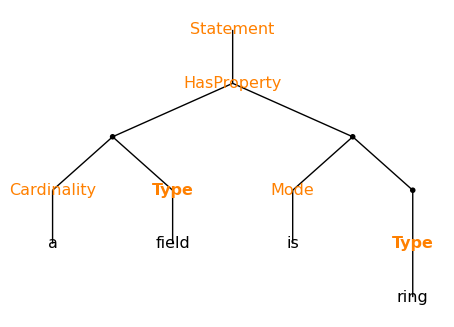

```mathematica
treeForm[parse1]
```

=Math Object;=Math Property;

### Examples

```mathematica
thm1="there exists a universal covering";
```

{Sentence[Statement→Exist[Math[Cardinality[a],Type[universal covering]]]]}

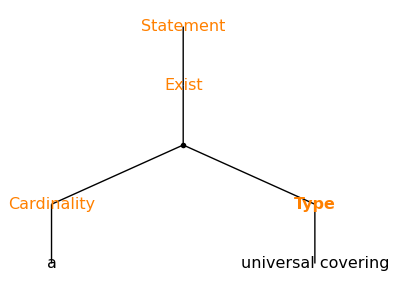

```mathematica
parseTree[thm1]
```

#### Examples cont’d

```mathematica
thm2="Suppose that the sequence $\\{s_i}$ is an admissible unbounded resolution of length $n>1$ of the projection $P_0$.";
```

{Sentence[Hypothesis→{HasProperty[Math[Cardinality[the],Type[sequence],Label[$\{s_i}$]],MathProperty[Mode[is],Math[Qualifiers[admissible],Type[resolution],Qualifiers[{of,Math[Type[length],Label[$n$],Qualifiers[{where,{Math[$n>1$]}}]]}]]]]}]}

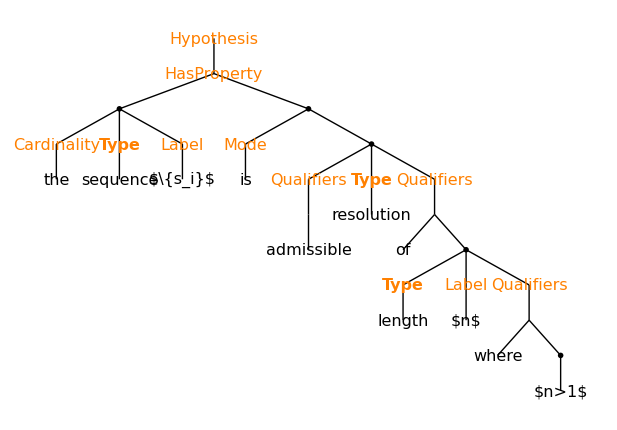

```mathematica
parseTree["suppose that the sequence $\\{s_i}$ is a admissible resolution of length $n$ where $n>1$"]
```

### Examples cont’d

```mathematica
thm3="Given any function $f$, there are infinitely many roots in $g(zeta(f))$.";
```

{Sentence[Hypothesis→{Math[Qualifiers[any],Type[function],Label[$f$]]},Statement→Exist[Math[Cardinality[infinitely many],Type[root],Qualifiers[{in,Math[Type[$g(zeta(f))$]]}]]]]}

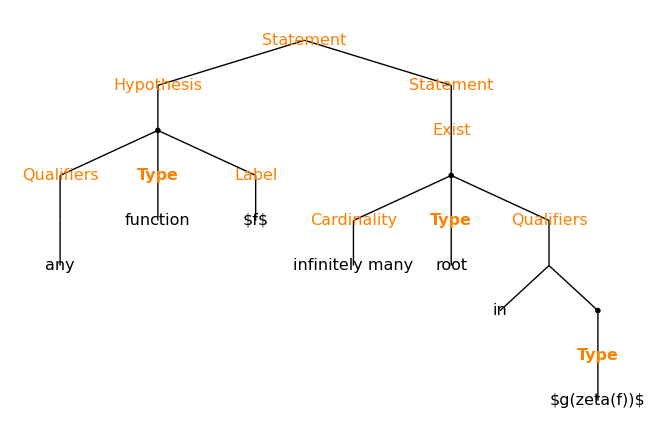

```mathematica
parseTree[thm3]
```

## Parser Implementation

Bottom-up parser. Uses context-free grammars.

Produces competing parses, ranked based on scores.

Uses lexicon, but can also infer token type from surrounding tokens for out-of-vocab words.

Recognizes the type such as qualifiers, cardinality, quantifiers, hypothesis, statement.

## Questions for you

How would you like us to distribute this?

Suggestions for improvements?

#### Examples cont’d

```mathematica
thm2="Suppose that the sequence $\\{s_i}$ is an admissible unbounded resolution of length $n>1$ of the projection $P_0$.";
```

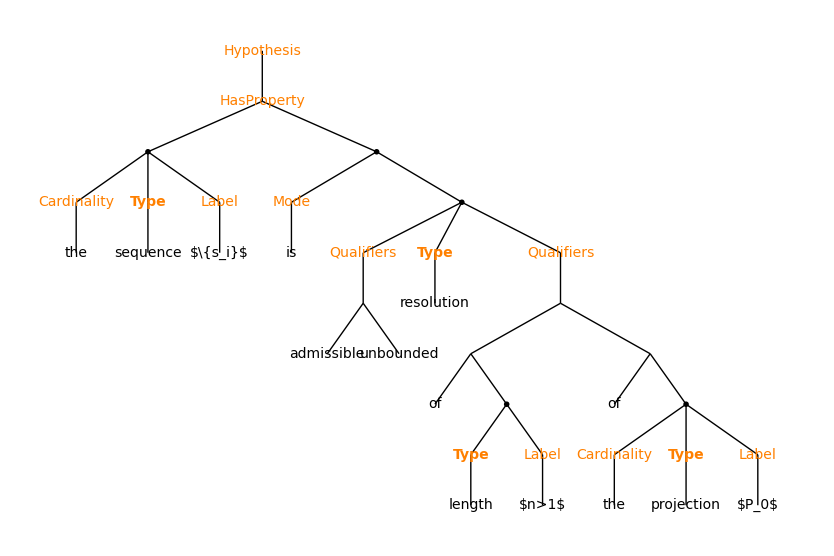

{Sentence[Hypothesis→{HasProperty[Math[Cardinality[the],Type[sequence],Label[$\{s_i}$]],MathProperty[Mode[is],Math[Qualifiers[admissible,unbounded],Type[resolution],Qualifiers[{of,Math[Type[length],Label[$n>1$]]},{of,Math[Cardinality[the],Type[projection],Label[$P_0$]]}]]]]}]}

```mathematica
parseTree[thm2]
```

#### Examples cont’d

{Sentence[Hypothesis→{HasProperty[Math[Type[avocadoes]],MathProperty[grow,Qualifiers[in,conjunction[Math[Type[california]],Math[Type[mexico]]]]]]}]}

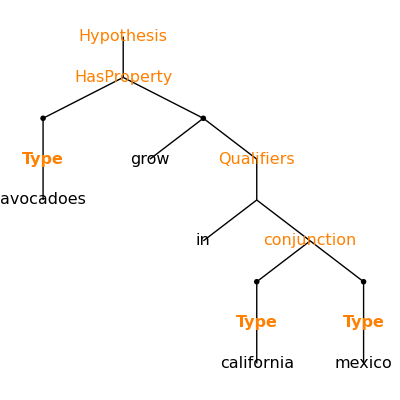

```mathematica
parseTree["suppose that avocadoes grow in california and mexico"]
```

### Examples cont’d

```mathematica
thm4="The fundamental group of any fake projective plane decomposes as a free nontrivial product with almagamation";
```

{Sentence[Statement→HasProperty[Math[Type[fundamental group],Qualifiers[{of,Math[Qualifiers[fake,any],Type[projective plane]]}]],MathProperty[decomposes,Qualifiers[as,Math[Qualifiers[free nontrivial],Type[product],Qualifiers[{with,Math[Type[almagamation]]}]]]]]]}

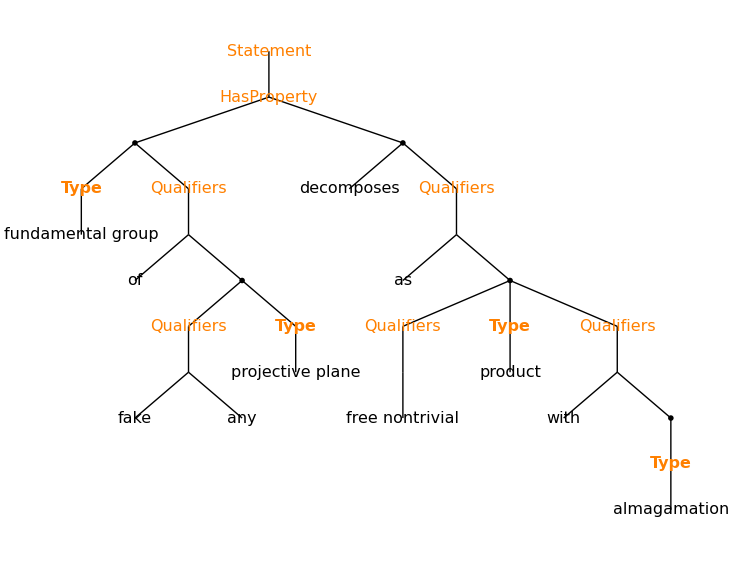

```mathematica
parseTree[thm4]
```

#### Examples cont’d

{Sentence[Statement→HasProperty[Math[Type[avocadoes]],MathProperty[grow,Qualifiers[in,conjunction[Math[Type[california]],Math[Type[mexico]]]]]]]}

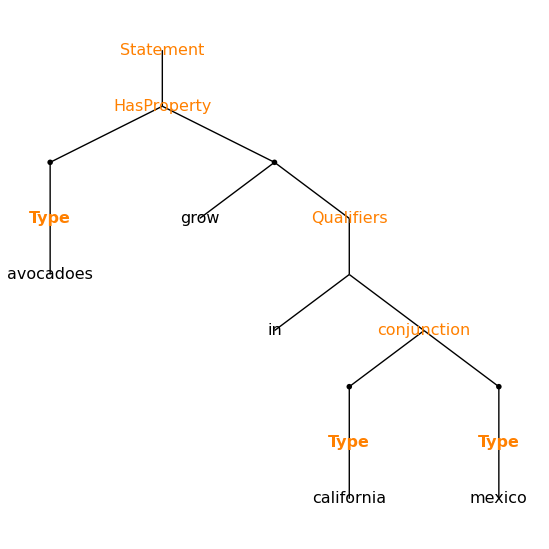

```mathematica
parseTree["avocadoes grow in california and mexico"]
```